```mathematica
dt=60/(118*4);

right={SoundNote["F#5",4 dt],SoundNote["B4",2 dt],SoundNote["B4",2 dt],SoundNote["D5",4 dt],SoundNote["F#5",4 dt],SoundNote["E5",2 dt],SoundNote["E5",dt],SoundNote["F#5",dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["B4",4 dt],SoundNote["F#5",4 dt],SoundNote["B4",2 dt],SoundNote["B4",2 dt],SoundNote["D5",4 dt],SoundNote["F#5",4 dt],SoundNote["A5",2 dt],SoundNote["E5",dt],SoundNote["F#5",dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["C#5",2 dt],SoundNote["A4",2 dt],SoundNote["F#5",4 dt],SoundNote["B4",2 dt],SoundNote["B4",2 dt],SoundNote["D5",4 dt],SoundNote["F#5",4 dt],SoundNote["E5",2 dt],SoundNote["E5",dt],SoundNote["F#5",dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["B4",4 dt],SoundNote["F#5",4 dt],SoundNote["B4",2 dt],SoundNote["B4",2 dt],SoundNote["D5",4 dt],SoundNote["F#5",4 dt],SoundNote["A5",2 dt],SoundNote["F#5",14 dt],(*开始*)SoundNote["B4",4 dt],SoundNote["B4",2 dt],SoundNote["A4",2 dt],SoundNote["B4",4 dt],SoundNote["B4",2 dt],SoundNote["D5",2 dt],SoundNote["D5",4 dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["B4",4 dt],SoundNote["B3",2 dt],SoundNote["C#3",2 dt],SoundNote[{"D4","D5"},4 dt],SoundNote["D5",2 dt],SoundNote["A4",2 dt],SoundNote["D5",2 dt],SoundNote["E5",2 dt],SoundNote["F#5",2 dt],SoundNote["A5",2 dt],SoundNote["A5",2 dt],SoundNote["F#5",2 dt],SoundNote["E5",4 dt],SoundNote["E5",dt],SoundNote["F#5",dt],SoundNote["E4",2 dt],SoundNote["F#4",2 dt],SoundNote["A4",2 dt](*2*),SoundNote["B5",2 dt],SoundNote["B5",2 dt],SoundNote["B5",2 dt],SoundNote["A5",2 dt],SoundNote["F#5",2 dt],SoundNote["F#5",4 dt],SoundNote["D5",2 dt](*3*),SoundNote["B4",2 dt],SoundNote["B4",2 dt],SoundNote["B4",2 dt],SoundNote["F#5",2 dt],SoundNote["E5",2 dt],SoundNote["D4",2 dt],SoundNote["D4",2 dt],SoundNote["E4",2 dt],SoundNote[{"F#4","F#5"},2 dt],SoundNote["F#5",2 dt],SoundNote["A5",2 dt],SoundNote["F#5",2 dt],SoundNote["E5",2 dt],SoundNote["F#5",2 dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["B4",4 dt],SoundNote[{"A4","D3"},4 dt],SoundNote[{"B4","B3"},8 dt](*第二段*),SoundNote[{"B4","F#4","D4"},4 dt],SoundNote[{"B4","D4"},2 dt],SoundNote[{"A4","C#4"},2 dt],SoundNote[{"B4","F#4","D4"},4 dt],SoundNote[{"B4","D4"},2 dt],SoundNote[{"D5","F#4"},2 dt],SoundNote[{"D5","B4","G4"},4 dt],SoundNote[{"E5","E4"},2 dt],SoundNote[{"D5","F#4"},2 dt],SoundNote[{"B4","D4"},8 dt],SoundNote[{"D5","A4","F#4"},4 dt],SoundNote[{"D5","F#4"},2 dt],SoundNote[{"A4","E4"},2 dt],SoundNote[{"D5","F#4"},2 dt],SoundNote[{"E5","A4"},2 dt],SoundNote[{"F#5","B4"},2 dt],SoundNote[{"A5","C#4"},2 dt],SoundNote[{"A5","A4"},2 dt],SoundNote["F#5",2 dt],SoundNote["E5",4 dt],SoundNote[{"F#4","B4","F#5"},8 dt],SoundNote[{"B5","B4"},2 dt],SoundNote["B5",2 dt],SoundNote["B5",2 dt],SoundNote["A5",2 dt],SoundNote[{"F#5","B4"},2 dt],SoundNote["F#5",4 dt],SoundNote["D4",2 dt],SoundNote[{"B4","F#4"},2 dt],SoundNote["B4",2 dt],SoundNote["B4",2 dt],SoundNote["F#5",2 dt],SoundNote["E5",8 dt],SoundNote[{"F#5","F#4"},2 dt],SoundNote[{"F#5","C#5"},2 dt],SoundNote[{"A5","F#5"},2 dt],SoundNote[{"F#5","C#5"},2 dt],SoundNote[{"E5","E4"},2 dt],SoundNote["F#5",2 dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote[{"F#4","B4"},4 dt],SoundNote[{"E4","A4"},4 dt],SoundNote[{"F#4","B4"},4 dt],SoundNote[{"D5","B4"},2 dt],SoundNote[{"F#5","E5"},2 dt],SoundNote[{"F#5","F#4"},2 dt],SoundNote[{"F#5","C#5"},2 dt],SoundNote[{"F#5","A5"},2 dt],SoundNote[{"F#5","C#5"},2 dt],SoundNote[{"F#5","C#5"},2 dt],SoundNote[{"E5","A5"},2 dt],SoundNote[{"E5","A5"},2 dt],SoundNote[{"F#5","B5"},2 dt],SoundNote[{"D6","F#5"},2 dt],SoundNote["B5",2 dt],SoundNote[{"E5","A5"},4 dt],SoundNote["B5",1/2*dt],SoundNote["D6",1/2*dt],SoundNote["B5",7*dt](*Climax*),SoundNote["D5",4 dt],SoundNote["D5",2 dt],SoundNote["C5",2 dt],SoundNote["D5",4 dt],SoundNote["F5",4 dt],SoundNote["G5",2 dt],SoundNote["A5",dt],SoundNote["G5",dt],SoundNote["F5",2 dt],SoundNote["G5",2 dt],SoundNote["A5",8 dt],SoundNote["D5",2 dt],SoundNote["D6",2 dt],SoundNote["D6",2 dt],SoundNote["C6",2 dt],SoundNote["G5",2 dt],SoundNote["A5",dt],SoundNote["G5",dt],SoundNote["F5",2 dt],SoundNote["G5",2 dt],SoundNote["A5",8 dt],SoundNote[{"A4","F4","C4"},4 dt],SoundNote["E4",4 dt],SoundNote["F5",4 dt],SoundNote["D5",2 dt],SoundNote["F5",2 dt],SoundNote["G5",4 dt],SoundNote["C5",4 dt],SoundNote["A5",2 dt],SoundNote["C6",2 dt],SoundNote["A5",2 dt],SoundNote["G5",2 dt],SoundNote["F5",6 dt],SoundNote["F5",2 dt],SoundNote["D5",2 dt],SoundNote["F5",2 dt],SoundNote["G5",2 dt],SoundNote["A5",2 dt],SoundNote["G5",2 dt],SoundNote["F5",2 dt],SoundNote["C5",2 dt],SoundNote["A4",2 dt],SoundNote[{"A4","D5"},10 dt],SoundNote["G4",2 dt],SoundNote["A4",2 dt],SoundNote["C5",2 dt],SoundNote["D5",4 dt],SoundNote["D5",2 dt],SoundNote["C5",2 dt],SoundNote["D5",4 dt],SoundNote["F5",4 dt],SoundNote["G5",2 dt],SoundNote["A5",dt],SoundNote["G5",dt],SoundNote["F5",2 dt],SoundNote["G5",2 dt],SoundNote["A5",8 dt],SoundNote["D6",2 dt],SoundNote["C6",2 dt],SoundNote["A5",2 dt],SoundNote["G5",2 dt],SoundNote["C6",2 dt],SoundNote["A5",2 dt],SoundNote["G5",2 dt],SoundNote["F5",2 dt],SoundNote["F5",12 dt],SoundNote["A4",dt],SoundNote["B4",dt],SoundNote["D5",dt],SoundNote["E5",dt],(*结尾*)SoundNote["F#5",4 dt],SoundNote["B4",2 dt],SoundNote["B4",2 dt],SoundNote["D5",4 dt],SoundNote["F#5",4 dt],SoundNote["E5",2 dt],SoundNote["E5",dt],SoundNote["F#5",dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["B4",4 dt],SoundNote["F#5",4 dt],SoundNote["B4",2 dt],SoundNote["B4",2 dt],SoundNote["D5",4 dt],SoundNote["F#5",4 dt],SoundNote["A5",2 dt],SoundNote["E5",dt],SoundNote["F#5",dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["C#5",2 dt],SoundNote["A4",2 dt],SoundNote["F#5",4 dt],SoundNote["B4",2 dt],SoundNote["B4",2 dt],SoundNote["D5",4 dt],SoundNote["F#5",4 dt],SoundNote["E5",2 dt],SoundNote["E5",dt],SoundNote["F#5",dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["E5",2 dt],SoundNote["D5",2 dt],SoundNote["B4",4 dt],SoundNote["F#5",4 dt],SoundNote["B4",2 dt],SoundNote["B4",2 dt],SoundNote["D5",4 dt],SoundNote["F#5",4 dt],SoundNote[{"A5","B4"},2 dt],SoundNote[{"F#5","C#5"},12 dt]};
```

```mathematica
f=Sound[right];
Export["3.wav",f]
```

3.wav

```mathematica
(*一个很厉害的人做的，网址http://www.kylen314.com/archives/1554*)
Hyperlink["下面的原网址","http://www.kylen314.com/archives/1554"]
```

[下面的原网址](http://www.kylen314.com/archives/1554)

```mathematica
Letter2Num[letter_]:=Switch[ToUpperCase[letter],"C",1,"D",2,"E",3,"F",4,"G",5,"A",6,"B",7];
Number2Letter[num_]:=Switch[num,1,"C",2,"D",3,"E",4,"F",5,"G",6,"A",7,"B"];
GetTone[base_,idx_]:=Module[{tone=Characters[base][[1]],step=Characters[base][[2]]},Number2Letter[Mod[Letter2Num[tone]-1+Mod[idx,7],7]+1]<>ToString[ToExpression[step]+Floor[idx/7]]]
GetTone["C5",5]
```

A5

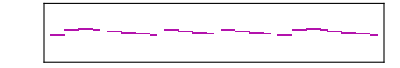

1.wav

```mathematica
GetMusicSingleTone[i_]:=Module[{},If[i==0,Play[0,{t,0,1}],SoundNote[GetTone["C4",i],1,"Violin"]]];
(*一闪一闪亮晶晶*)
xingxing=Flatten[Riffle[{IntegerDigits[1155665],IntegerDigits[4433221],IntegerDigits[5544332],IntegerDigits[5544332],IntegerDigits[11556654433221]},0]];
f=Sound[Table[GetMusicSingleTone[xingxing[[i]]],{i,1,Length[xingxing]}],20]
Export["1.wav",f]
```

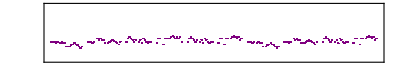

1.wav

```mathematica
FromFlashGame[pu_]:=Module[{str=Characters[ToUpperCase[pu]],music={}},For[i=1,i<Length[str],i++,If[ToCharacterCode["Z"][[1]]≥ToCharacterCode[str[[i]]][[1]]≥ToCharacterCode["A"][[1]],music=Append[music,SoundNote[GetTone["C1",ToCharacterCode[str[[i]]][[1]]-ToCharacterCode["A"][[1]]],1]],If[ToCharacterCode[str[[i]]][[1]]==32,music=Append[music,Play[0,{t,0,1}]],]]];
music]
f=Sound[FromFlashGame["QQQPQ PQPPM MNOPONMLM 
  QQQPQ TSTSSP PQRSRQPOQ 
  QTUTSQS QSPTSQPQQ 
  PTT OTT TUVUTUTUQ 
  QTUTSQS QSPTSQPQQ 
  PTT OTT TUVUTUST 
  QQQPQ PQPPM MNOPONMLM 
  QQQPQ TSTSSP PQRSRQPOQ 
  QTUTSQS QSPTSQPQQ 
  PTT OTT TUVUTUST "],60]
Export["1.wav",f]
```

```mathematica
kanong={{10,"-",9,"-"},{8,"-",7,"-"},{6,"-",5,"-"},{6,"-",7,"-"},{8,"-",7,"-"},{6,"-",5,"-"},{4,"-",3,"-"},{4,"-",2,"-"},{{8,7,8,1},{0,5,2,3}},{{1,8,7,6},{7,10,12,13}},{{11,10,9,11},{11,10,8,7}},{{6,5,4,3},{2,4,3,2}},{{1,2,3,4},{5,2,5,4}},{{3,6,5,4},{5,4,3,2}},{{1,-1,6,7},{8,7,6,5}},{{4,3,2,6},{5,6,5,4}},{3,10,9,"-"},{8,"-",9,"-"},{8,10,9,11},{{12,{10,11}},{12,{10,11}},{12,5,6,7},{8,9,10,11}},{{10,{8,9}},{10,{3,4}},{5,6,5,4},{5,3,4,5}},{{4,{6,5}},{4,{3,2}},{3,2,1,2},{3,4,5,6}},{{4,{6,5}},{6,{7,8}},{5,6,7,8},{9,10,11,12}},{{10,{8,9}},{10,{9,8}},{9,7,8,9},{10,9,8,7}},{{8,{6,7}},{8,{1,2}},{3,4,3,2},{3,8,7,8}},{{6,{8,7}},{6,{5,4}},{5,4,3,4},{5,6,7,1}},{{6,{8,7}},{8,{7,6}},{7,8,9,8},{7,8,6,7}},{{9,3,4,3},{2,9,10,9}},{{8,3,1,6},{5,-2,-3,-2}},{{-1,6,7,6},{7,-2,-3,-2}},{{-1,6,5,6},{7,7,6,7}},{{1,8,9,8},{7,0,1,0}},{{-1,6,5,6},{7,0,3,2}},{{1,8,9,11},{10,3,5,10}},{{8,11,10,11},{9,5,4,5}},{{3,{8,7}},{8,3},{5,{5,6}},{7,5}},{{3,{8,9}},{10,8},{10,{10,9}},{8,7}},{{3,{7,8}},{10,8},{10,{10,9}},{8,7}},{{6,{6,5}},{6,7},{8,{10,9}},{8,10}},{{4,{1,7}},{6,6},{5,2},{5,5}},{3,10,{10,11},{10,9}},{8,8,{8,9},{8,7}},{6,"-",8,"-"},{{{8,7},{6,7}},{5,{5}}},{{5,{5}},{{5,6},{5,4}}},{{3,{3}},{{3,4},{3,2}}},{{{8,7},{6,7}},{5,{5}}},{4,8,7,7},{12,"-",5,4},{10,"-",10,9},{8,"-","-",1},{8,"-",7,"-"},{8,1,0,7},{6,-1,-2,5},{4,11,10,3},{2,6,2,8},{9,3,2,8},{8,1,0,7},{6,13,12,5},{4,8,5,8},{9,"-","-","-"}};
```

```mathematica
DesposeMusic[music_,depth_]:=Module[{rr={},idx},For[idx=1,idx<=Length[music],idx++,If[Head[music[[idx]]]===List,AppendTo[rr,DesposeMusic[music[[idx]],depth/Length[music]]],AppendTo[rr,If[music[[idx]]==="-",Play[0,{t,0,depth/Length[music]}],SoundNote[GetTone["C3",music[[idx]]],depth/Length[music]]]]]];
Return[rr];]
f=Sound[DesposeMusic[kanong,1000],120]
Export["1.wav",f]
```

Transpose::nmtx: {{{56.5573,43},{58.5245,43},{56.3114,45},{56.8032,45},{58.2786,45},{58.7704,45},{105.246,45},«37»,{48.0737,52},{48.5655,52},{54.0983,52},{64.6721,52},{77.9508,52},{90.2459,52},«349»},{«1»}} 的前两层无法转置.

-Graphics-

1.wav